```mathematica
<<GRSpectral.m
```

```mathematica
restart[];
eqw=(c z bt[z])/L^2+(c (-1+z) z bt'[z])/L^2+(rh^2 w[z] (4/L^2+(a z^4)/rh^2+(2 qA^2 (-1+z)^2 κ)/f[z]+(2 z^2 (-k^2 L^2+z f'[z]))/rh^2))/(2 L^2 z^2)+(z (2 f[z]+z f'[z]) w'[z])/L^2+(z^2 f[z] w''[z])/L^2/.k^2->k2;
eqbt=-k^2 bt[z]+(c z^2 f[z] w[z])/(L^2 (-1+z))+(2 z^2 f[z] bt'[z])/(L^2 (-1+z))+(c z^3 f[z] w'[z])/(L^2 (-1+z))+(z^2 f[z] bt''[z])/L^2/.k^2->k2;
f[z_]:=rh^2/(L^2 z^2)(1-z^3)+(μ^2 z^2)/4(1-1/z);
T[rh_]:=rh/(4Pi)(3/L^2-μ^2/(4 rh^2));
bdylist1={w[z],bt[z]};
bdylist2={(4 c L^2 bt[z]+(-4 rh^2+L^2 (2a+μ^2)) w[z]+(-12 rh^2+L^2 μ^2) w'[z])/(4 L^4),-((12 rh^2-L^2 μ^2) (2 bt'[z]+c (w[z]+w'[z])))/(4 L^4)};
eqProcess[{w[z],bt[z]},{eqw,eqbt},{{z==0,bdylist1},{z==1,bdylist2}},k2];
mat=mat/.z->zaux12;
output:=listFormat[{Sqrt[eig//Chop//positive],N@T[rh]},1]ᵀ;
```

```mathematica
L=1/2;rh=0.152;a=4;κ=1;c=2.34;qA=1;μ=1;mv2=0;
```

```mathematica
spNDEigen[z,linearMap[{0,1}],100]
```

{{1.44319,0.0142653},{0.830197,0.0142653}}

```mathematica
data=spNDEigen[z,linearMap[{0,1}],100,{rh,0.14436,0.153,0.0001}];
```

```mathematica
sdata=Sort[Flatten[data,1],#1⟦1⟧<#2⟦1⟧&];
```

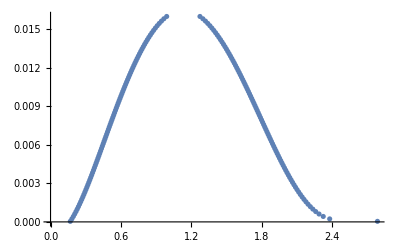

```mathematica
ListPlot[sdata]
```

```mathematica
dataf=Interpolation[sdata];
```

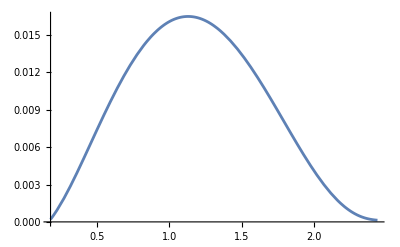

```mathematica
Plot[dataf[k],{k,0.18,2.43806}]
```

```mathematica
Tc=0.016483288606347273;
```

```mathematica
T[0.1532]/Tc
```

0.997157